## Definiciones

```mathematica
PositiveParitySubspaceBasis[L_]:=DeleteDuplicatesBy[Tuples[{0,1},L],First[Sort[{#,Reverse[#]}]]&]
```

```mathematica
ℰ[ρ_,t_]:=MatrixPartialTrace[U[t].KroneckerProduct[ρ,Dyad[ψ],ρ].ConjugateTranspose[U[t]],2,{2,2^(L-2),2}]
```

```mathematica
ClearAll[𝒟]
𝒟[t_]:=1/2Chop[Total[KroneckerProduct[ℰ[Dyad[#1,#2],t],Dyad[#1,#2]]&@@@{{{1,0},{1,0}},{{1,0},{0,1}},{{0,1},{1,0}},{{0,1},{0,1}}}]]
```

## Cálculo

```mathematica
hx=1.;
hz=0.5;
J=1.;
L=3;

H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvalues, eigenvectors} = Chop[Eigensystem[H]];

(* Calcular la matriz de cambio de base de la de eigenenergías a la computacional *)
P = Transpose[eigenvectors];

(* Operador de evolución *)
ClearAll[U];
U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvalues*t]].ConjugateTranspose[P];

ψ=RandomChainProductState[L-2];
```

```mathematica
ℰ[ρ_,t_]:=MatrixPartialTrace[U[t].KroneckerProduct[ρ,Dyad[ψ],ρ].ConjugateTranspose[U[t]],2,{2,2^(L-2),2}]
```

```mathematica
ℰ[Dyad[{0,1}],0.]//Chop//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1.)

```mathematica
ClearAll[𝒟]
𝒟[t_]:=1/2Chop[Total[KroneckerProduct[ℰ[Dyad[#1,#2],t],Dyad[#1,#2]]&@@@{{{1,0},{1,0}},{{1,0},{0,1}},{{0,1},{1,0}},{{0,1},{0,1}}}]]
```

```mathematica
Chop[Eigenvalues[𝒟[#]]]&/@Range[0,10,0.1]
```

{{1.,0,0,0,0,0,0,0},{0.968664,0.0313363,0,0,0,0,0,0},{0.875596,0.124404,0,0,0,0,0,0},{0.738413,0.261587,0,0,0,0,0,0},{0.589018,0.410982,0,0,0,0,0,0},{0.540609,0.459391,0,0,0,0,0,0},{0.621467,0.378533,0,0,0,0,0,0},{0.648358,0.351642,0,0,0,0,0,0},{0.63214,0.36786,0,0,0,0,0,0},{0.602807,0.397193,0,0,0,0,0,0},{0.596424,0.403576,0,0,0,0,0,0},{0.608329,0.391671,0,0,0,0,0,0},{0.610656,0.389344,0,0,0,0,0,0},{0.601964,0.398036,0,0,0,0,0,0},{0.6044,0.3956,0,0,0,0,0,0},{0.627533,0.372467,0,0,0,0,0,0},{0.650898,0.349102,0,0,0,0,0,0},{0.657366,0.342634,0,0,0,0,0,0},{0.646167,0.353833,0,0,0,0,0,0},{0.632607,0.367393,0,0,0,0,0,0},{0.641284,0.358716,0,0,0,0,0,0},{0.680649,0.319351,0,0,0,0,0,0},{0.736867,0.263133,0,0,0,0,0,0},{0.792684,0.207316,0,0,0,0,0,0},{0.830799,0.169201,0,0,0,0,0,0},{0.834888,0.165112,0,0,0,0,0,0},{0.795315,0.204685,0,0,0,0,0,0},{0.716263,0.283737,0,0,0,0,0,0},{0.627393,0.372607,0,0,0,0,0,0},{0.618213,0.381787,0,0,0,0,0,0},{0.688075,0.311925,0,0,0,0,0,0},{0.740937,0.259063,0,0,0,0,0,0},{0.751482,0.248518,0,0,0,0,0,0},{0.726188,0.273812,0,0,0,0,0,0},{0.69091,0.30909,0,0,0,0,0,0},{0.678187,0.321813,0,0,0,0,0,0},{0.692949,0.307051,0,0,0,0,0,0},{0.708368,0.291632,0,0,0,0,0,0},{0.702275,0.297725,0,0,0,0,0,0},{0.6668,0.3332,0,0,0,0,0,0},{0.607001,0.392999,0,0,0,0,0,0},{0.565833,0.434167,0,0,0,0,0,0},{0.62533,0.37467,0,0,0,0,0,0},{0.70795,0.29205,0,0,0,0,0,0},{0.769909,0.230091,0,0,0,0,0,0},{0.79805,0.20195,0,0,0,0,0,0},{0.793107,0.206893,0,0,0,0,0,0},{0.767462,0.232538,0,0,0,0,0,0},{0.73881,0.26119,0,0,0,0,0,0},{0.719193,0.280807,0,0,0,0,0,0},{0.709955,0.290045,0,0,0,0,0,0},{0.710891,0.289109,0,0,0,0,0,0},{0.724272,0.275728,0,0,0,0,0,0},{0.742604,0.257396,0,0,0,0,0,0},{0.745979,0.254021,0,0,0,0,0,0},{0.716886,0.283114,0,0,0,0,0,0},{0.656895,0.343105,0,0,0,0,0,0},{0.615756,0.384244,0,0,0,0,0,0},{0.670404,0.329596,0,0,0,0,0,0},{0.754277,0.245723,0,0,0,0,0,0},{0.808599,0.191401,0,0,0,0,0,0},{0.81853,0.18147,0,0,0,0,0,0},{0.795039,0.204961,0,0,0,0,0,0},{0.766272,0.233728,0,0,0,0,0,0},{0.754753,0.245247,0,0,0,0,0,0},{0.751296,0.248704,0,0,0,0,0,0},{0.7301,0.2699,0,0,0,0,0,0},{0.678879,0.321121,0,0,0,0,0,0},{0.606971,0.393029,0,0,0,0,0,0},{0.556195,0.443805,0,0,0,0,0,0},{0.58945,0.41055,0,0,0,0,0,0},{0.633361,0.366639,0,0,0,0,0,0},{0.659624,0.340376,0,0,0,0,0,0},{0.672865,0.327135,0,0,0,0,0,0},{0.678335,0.321665,0,0,0,0,0,0},{0.677019,0.322981,0,0,0,0,0,0},{0.677744,0.322256,0,0,0,0,0,0},{0.70199,0.29801,0,0,0,0,0,0},{0.753257,0.246743,0,0,0,0,0,0},{0.804274,0.195726,0,0,0,0,0,0},{0.824335,0.175665,0,0,0,0,0,0},{0.796051,0.203949,0,0,0,0,0,0},{0.720416,0.279584,0,0,0,0,0,0},{0.621899,0.378101,0,0,0,0,0,0},{0.595803,0.404197,0,0,0,0,0,0},{0.679625,0.320375,0,0,0,0,0,0},{0.755716,0.244284,0,0,0,0,0,0},{0.795923,0.204077,0,0,0,0,0,0},{0.800339,0.199661,0,0,0,0,0,0},{0.781292,0.218708,0,0,0,0,0,0},{0.758562,0.241438,0,0,0,0,0,0},{0.750319,0.249681,0,0,0,0,0,0},{0.757052,0.242948,0,0,0,0,0,0},{0.759726,0.240274,0,0,0,0,0,0},{0.73763,0.26237,0,0,0,0,0,0},{0.68137,0.31863,0,0,0,0,0,0},{0.597192,0.402808,0,0,0,0,0,0},{0.545236,0.454764,0,0,0,0,0,0},{0.627713,0.372287,0,0,0,0,0,0},{0.709595,0.290405,0,0,0,0,0,0},{0.76873,0.23127,0,0,0,0,0,0}}

## Otros parámetros

```mathematica
hx=1.;
hz=3.;
J=1.;
L=7;

H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvalues, eigenvectors} = Chop[Eigensystem[H]];

(* Calcular la matriz de cambio de base de la de eigenenergías a la computacional *)
P = Transpose[eigenvectors];

(* Operador de evolución *)
ClearAll[U];
U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvalues*t]].ConjugateTranspose[P];

basisevenparity=Normalize[SparseArray[{FromDigits[#,2]+1->1.,FromDigits[Reverse[#],2]+1->1.},2^(L-2)]]&/@PositiveParitySubspaceBasis[L-2];
ψ=With[{randomcoeff=RandomVariate[CircularUnitaryMatrixDistribution[Length[basisevenparity]]][[All,1]]},randomcoeff.basisevenparity];
```

```mathematica
t=Range[0,50,0.5];
```

```mathematica
Chop[Eigenvalues[𝒟[#]]]&/@t[[1;;10]]
```

{{1.,0,0,0,0,0,0,0},{0.676444,0.28296,0.0279726,0.0118515,0.000526725,0.000205383,0.0000296904,0.0000101194},{0.487389,0.435114,0.0361252,0.0336893,0.00376768,0.00340557,0.00031256,0.000196873},{0.790751,0.175833,0.0166042,0.0073438,0.00530814,0.00369626,0.000390384,0.0000728936},{0.877134,0.0878319,0.0184737,0.00784961,0.00414598,0.00407833,0.000343296,0.00014265},{0.525858,0.41095,0.0313543,0.0245213,0.00404709,0.00259141,0.00037842,0.000300145},{0.558927,0.387049,0.0300269,0.020789,0.00154569,0.00131214,0.000222832,0.000127941},{0.769877,0.202488,0.0120633,0.00859403,0.00520166,0.00157798,0.000128771,0.0000699065},{0.727805,0.23927,0.0224234,0.0077218,0.00149971,0.00110074,0.000131392,0.0000473649},{0.513733,0.396845,0.0419154,0.0416408,0.00296771,0.00264489,0.000162061,0.0000912662}}

```mathematica
choieigenvals=Transpose[Chop[Eigenvalues[𝒟[#]][[1;;2]]]&/@t];
```

Caótico

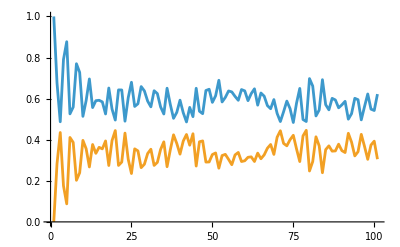

```mathematica
ListPlot[choieigenvals,Joined->True]
```

Regular

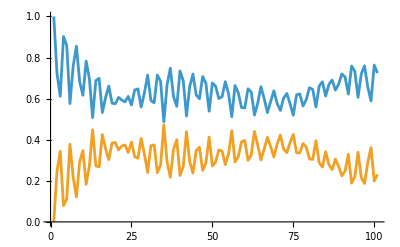

```mathematica
ListPlot[choieigenvals,Joined->True]
```

```mathematica
L=3;
basisevenparity=Normalize[SparseArray[{FromDigits[#,2]+1->1.,FromDigits[Reverse[#],2]+1->1.},2^3]]&/@PositiveParitySubspaceBasis[3];
ψ=With[{randomcoeff=RandomVariate[CircularUnitaryMatrixDistribution[Length[basisevenparity]]][[All,1]]},randomcoeff.basisevenparity]
```

{-0.117386+0.0888846 ⅈ,0.0784347+0.116791 ⅈ,-0.562148-0.0925824 ⅈ,-0.205013+0.118252 ⅈ,0.0784347+0.116791 ⅈ,-0.132181+0.622335 ⅈ,-0.205013+0.118252 ⅈ,0.26313-0.167675 ⅈ}

```mathematica
MatrixForm[ρ=Chop[ℰ[Dyad[{1,0}],50.4]]]
```

(0.855006 | 0.169324-0.0100397 ⅈ | 0.169324-0.0100397 ⅈ | 0.0357155-0.00805159 ⅈ
0.169324+0.0100397 ⅈ | 0.0689041 | 0.0490276 | 0.017619-0.00280543 ⅈ
0.169324+0.0100397 ⅈ | 0.0490276 | 0.0689041 | 0.017619-0.00280543 ⅈ
0.0357155+0.00805159 ⅈ | 0.017619+0.00280543 ⅈ | 0.017619+0.00280543 ⅈ | 0.00718618)

```mathematica
Chop[Eigenvalues[𝒟[50.4]]]//Sort
```

{0.000169555,0.000452459,0.00401602,0.00440008,0.013002,0.0367815,0.400863,0.540316}

```mathematica
KroneckerProduct[MatrixPartialTrace[ρ,1,2],MatrixPartialTrace[ρ,2,2]]//MatrixForm
```

(0.853609+0. ⅈ | 0.172719-0.0118677 ⅈ | 0.172719-0.0118677 ⅈ | 0.0347828-0.00480262 ⅈ
0.172719+0.0118677 ⅈ | 0.0703006+0. ⅈ | 0.0351128+1.93887×10^-12 ⅈ | 0.0142246-0.000977391 ⅈ
0.172719+0.0118677 ⅈ | 0.0351128-1.93887×10^-12 ⅈ | 0.0703006+0. ⅈ | 0.0142246-0.000977391 ⅈ
0.0347828+0.00480262 ⅈ | 0.0142246+0.000977391 ⅈ | 0.0142246+0.000977391 ⅈ | 0.00578974+0. ⅈ)

```mathematica
BlochVector[MatrixPartialTrace[ρ,1,2]]
BlochVector[MatrixPartialTrace[ρ,2,2]]
```

{0.373887,0.0256903,0.847819}

{0.373887,0.0256903,0.847819}

## Algo raro

```mathematica
hx=1.;
hz=3.;
J=1.;
L=7;

H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvalues, eigenvectors} = Chop[Eigensystem[H]];

(* Calcular la matriz de cambio de base de la de eigenenergías a la computacional *)
P = Transpose[eigenvectors];

(* Operador de evolución *)
ClearAll[U];
U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvalues*t]].ConjugateTranspose[P];

ψ=RandomChainProductState[L-2];
```

```mathematica
t=Range[0,50,0.5];
```

```mathematica
Chop[Eigenvalues[𝒟[#]]]&/@t[[1;;10]]
```

{{1.,0,0,0,0,0,0,0},{0.692913,0.271387,0.025501,0.0100185,0.0000976719,0.0000737329,5.0545×10^-6,4.71756×10^-6},{0.538638,0.409829,0.0259965,0.0201955,0.00359119,0.00146729,0.000158793,0.000123077},{0.844044,0.121925,0.0202414,0.00621599,0.00483152,0.00229952,0.000342969,0.0000990976},{0.885684,0.0755521,0.0182252,0.0117213,0.00561728,0.00266238,0.000329283,0.000208941},{0.545519,0.376017,0.0438277,0.0268803,0.00570614,0.0015627,0.000282925,0.000204185},{0.590247,0.346569,0.0374901,0.0212548,0.00329296,0.000918439,0.000148395,0.0000797051},{0.862221,0.112031,0.0114488,0.0080784,0.00484354,0.00117693,0.00013177,0.0000689492},{0.754782,0.223404,0.0146229,0.00509596,0.00143106,0.000602377,0.000047779,0.0000130942},{0.483595,0.43917,0.0392385,0.0338045,0.0028085,0.00110335,0.000159786,0.000120301}}

```mathematica
choieigenvals=Transpose[Chop[Eigenvalues[𝒟[#]][[1;;2]]]&/@t];
```

Caótico

```mathematica
ListPlot[choieigenvals,Joined->True]
```

-Graphics-

Regular

```mathematica
ListPlot[choieigenvals,Joined->True]
```

-Graphics-

```mathematica
L=3;
basisevenparity=Normalize[SparseArray[{FromDigits[#,2]+1->1.,FromDigits[Reverse[#],2]+1->1.},2^3]]&/@PositiveParitySubspaceBasis[3];
ψ=With[{randomcoeff=RandomVariate[CircularUnitaryMatrixDistribution[Length[basisevenparity]]][[All,1]]},randomcoeff.basisevenparity]
```

{-0.117386+0.0888846 ⅈ,0.0784347+0.116791 ⅈ,-0.562148-0.0925824 ⅈ,-0.205013+0.118252 ⅈ,0.0784347+0.116791 ⅈ,-0.132181+0.622335 ⅈ,-0.205013+0.118252 ⅈ,0.26313-0.167675 ⅈ}